## Direct Interpolation @2.76 TeV

```mathematica
f=Interpolation[{{0.2,{9.113*10^2,1.459,7.679}},{5.5,{2.209*10^4,0.5635,5.240}}}]
```

Interpolation::inhr: 要求的阶数太高；阶数已经被降低为 {1}.

InterpolatingFunction[…]

```mathematica
f[2.76]
```

{11141.,1.02646,6.50092}

## Logarithmic Interpolation @2.76 TeV

gluon(first g represents function)

```mathematica
gg=Interpolation[{{Log[0.2],{Log[4.455*^3],Log@1.7694,Log@8.610}},{Log[5.5],{Log[1.229*^5],Log@0.7717,Log@5.600}}}];
gg[Log[2.76]];
Exp[%]
```

Interpolation::inhr: 要求的阶数太高；阶数已经被降低为 {1}.

{61632.9,0.917118,6.12428}

```mathematica
gg=Interpolation[{{Log[10,0.2],{Log[10,4.455*^3],Log[10,1.7694],Log[10,8.610]}},{Log[10,5.5],{Log[10,1.229*^5],Log[10,0.7717],Log[10,5.600]}}}];
gg[Log[10,2.76]];
10^%
```

Interpolation::inhr: 要求的阶数太高；阶数已经被降低为 {1}.

{61632.9,0.917118,6.12428}

u quark

```mathematica
gu=Interpolation[{{Log[0.2],{Log[9.113*10^2],Log@1.459,Log@7.679}},{Log[5.5],{Log[2.209*10^4],Log@0.5635,Log@5.240}}}]
```

Interpolation::inhr: 要求的阶数太高；阶数已经被降低为 {1}.

InterpolatingFunction[…]

```mathematica
gu[Log[2.76]];
Exp[%]
```

{11380.,0.686835,5.67364}

d quark

```mathematica
gd=Interpolation[{{Log[0.2],{Log[9.596*^2],Log@1.467,Log@7.662}},{Log[5.5],{Log[2.493*^4],Log@0.5522,Log@5.223}}}];
gd[Log[2.76]];
Exp[%]
```

Interpolation::inhr: 要求的阶数太高；阶数已经被降低为 {1}.

{12659.2,0.676673,5.65645}

ubar quark

```mathematica
gubar=Interpolation[{{Log[0.2],{Log[2.031*^2],Log@1.767,Log@8.546}},{Log[5.5],{Log[4.581*^3],Log@0.7248,Log@5.437}}}];
Exp@gubar[Log[2.76]]
```

Interpolation::inhr: 要求的阶数太高；阶数已经被降低为 {1}.

{2395.61,0.872444,5.97339}

dbar quark

```mathematica
gdbar=Interpolation[{{Log[0.2],{Log[2.013*^2],Log@1.759,Log@8.566}},{Log[5.5],{Log[4.317*^3],Log@0.7343,Log@5.448}}}];
Exp@gdbar[Log[2.76]]
```

Interpolation::inhr: 要求的阶数太高；阶数已经被降低为 {1}.

{2281.38,0.880656,5.98587}

s & sbar quark

```mathematica
gs=Interpolation[{{Log[0.2],{Log[1.038*^2],Log@1.868,Log@8.642}},{Log[5.5],{Log[1.662*^3],Log@0.9064,Log@5.548}}}];
Exp@gs[Log[2.76]]
```

Interpolation::inhr: 要求的阶数太高；阶数已经被降低为 {1}.

{933.358,1.05356,6.08389}

Summary(note first row and the last one)

```mathematica
Exp@{gg[Log[2.76]],gu[Log[2.76]],gd[Log[2.76]],gubar[Log[2.76]],gdbar[Log[2.76]],gs[Log[2.76]]}
```

{{61632.9,0.917118,6.12428},{11380.,0.686835,5.67364},{12659.2,0.676673,5.65645},{2395.61,0.872444,5.97339},{2281.38,0.880656,5.98587},{933.358,1.05356,6.08389}}

## Logarithmic Interpolation @5.02 TeV

```mathematica
parameters502=Exp@{gg[Log[5.02]],gu[Log[5.02]],gd[Log[5.02]],gubar[Log[5.02]],gdbar[Log[5.02]],gs[Log[5.02]]}
```

{{112164.,0.789547,5.66677},{20232.4,0.578466,5.29547},{22790.,0.567268,5.27844},{4204.1,0.742817,5.50517},{3967.33,0.752189,5.51636},{1539.73,0.924641,5.61617}}

```mathematica
Export["fik_parameters_502.txt",parameters502]
```

parameters_502.txt

## Plot fik

### u quark

```mathematica
u02[p_]:=2.5 911.3/(1+p/1.459)^7.679;u276[p_]:=2.5 11380/(1+p/0.687)^5.67;u502[p_]:=2.5 20232.4/(1+p/0.578)^5.295;u55[p_]:=2.5 22090/(1+p/0.5635)^5.24;
ug276[p_]:=Exp[(5.5-2.76)/(5.5-0.2)(Log@u02[p]-Log@u55[p])+Log@u55[p]];(*guess 2.76 TeV*)
ug502[p_]:=Exp[(5.5-5.02)/(5.5-0.2)(Log@u02[p]-Log@u55[p])+Log@u55[p]];(*guess 5.02 TeV*)
```

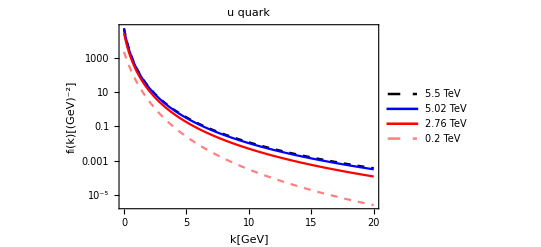

```mathematica
fiku=Show[{LogPlot[{u55[p],u502[p],u276[p],u02[p]},{p,0,20},PlotLegends->Placed[LineLegend[{
Directive[{Black,Dashed},Thickness[0.01]],
Directive[Blue,Thickness[0.01]],
Directive[Red,Thickness[0.01]],
Directive[{Pink,Dashed},Thickness[0.01]]},{Text@Style["5.5 TeV",Bold,FontSize->20],Text@Style["5.02 TeV",Bold,FontSize->20],Text@Style["2.76 TeV",Bold,FontSize->20],Text@Style["0.2 TeV",Bold,FontSize->20]}],{Right,Top}],PlotStyle->{{Black,Dashed},Blue,Red,{Pink,Dashed}},PlotLabel->"u quark"],LabelStyle->Directive[Black,Bold,20]},FrameLabel->{"k[GeV]","f_i(k)[(GeV)^-2]"},
LabelStyle->Directive[Black,Bold,20] ,FrameTicksStyle->{{Black,Thick},{Black,Thick}},Frame->True,FrameStyle->Thick]
```

```mathematica
Export["fiku.png",Show[fiku,ImageSize->Large],ImageResolution->500]
```

fiku.png

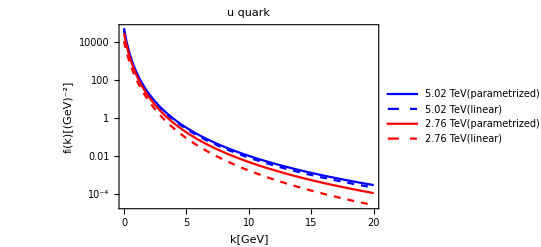

```mathematica
Show[{LogPlot[{u502[p],ug502[p],u276[p],ug276[p]},{p,0,20},PlotLegends->Placed[{"5.02 TeV(parametrized)","5.02 TeV(linear)","2.76 TeV(parametrized)","2.76 TeV(linear)"},{Right,Top}],PlotStyle->{Blue,{Blue,Dashed},Red,{Red,Dashed}},PlotLabel->"u quark"]},FrameLabel->{"k[GeV]","f_i(k)[(GeV)^-2]"},
LabelStyle->Directive[Black,Bold,12] ,FrameTicksStyle->{{Black,Thick},{Black,Thick}},Frame->True,FrameStyle->Thick]
```

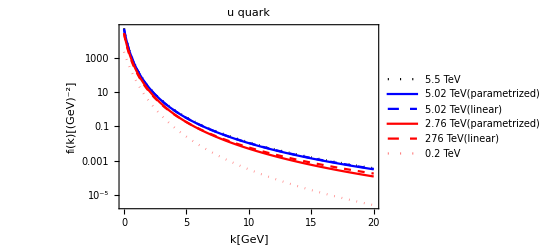

```mathematica
Show[{LogPlot[{u55[p],u502[p],ug502[p],u276[p],ug276[p],u02[p]},{p,0,20},PlotLegends->{"5.5 TeV","5.02 TeV(parametrized)","5.02 TeV(linear)","2.76 TeV(parametrized)","276 TeV(linear)","0.2 TeV"},PlotStyle->{{Black,Dotted},Blue,{Blue,Dashed},Red,{Red,Dashed},{Pink,Dotted}},PlotLabel->"u quark"]},FrameLabel->{"k[GeV]","f_i(k)[(GeV)^-2]"},
LabelStyle->Directive[Black,Bold,20] ,FrameTicksStyle->{{Black,Thick},{Black,Thick}},Frame->True,FrameStyle->Thick]
```

## conclusion:ln fik is not proportional to √s_NN. Now guess ln fik is proportional to ln √s_NN, i.e. fik is proportional to √s_NN.

```mathematica
u02[p_]:=2.5 911.3/(1+p/1.459)^7.679;u276[p_]:=2.5 11380/(1+p/0.687)^5.67;u502[p_]:=2.5 20232.4/(1+p/0.578)^5.295;u55[p_]:=2.5 22090/(1+p/0.5635)^5.24;
ug276[p_]:=(5.5-2.76)/(5.5-0.2)(u02[p]-u55[p])+u55[p];(*guess 2.76 TeV*)
ug502[p_]:=(5.5-5.02)/(5.5-0.2)(u02[p]-u55[p])+u55[p];(*guess 5.02 TeV*)
```

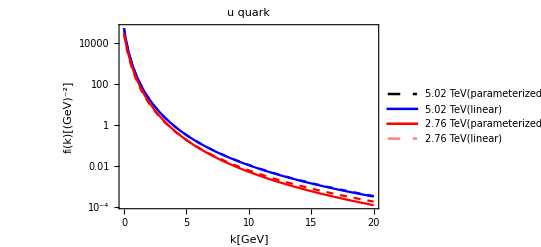

```mathematica
compareu=Show[{LogPlot[{u502[p],ug502[p],u276[p],ug276[p]},{p,0,20},PlotLegends->Placed[LineLegend[{
Directive[{Black,Dashed},Thickness[0.01]],
Directive[Blue,Thickness[0.01]],
Directive[Red,Thickness[0.01]],
Directive[{Pink,Dashed},Thickness[0.01]]},{Text@Style["5.02 TeV(parameterized)",Bold,FontSize->20],Text@Style["5.02 TeV(linear)",Bold,FontSize->20],Text@Style["2.76 TeV(parameterized)",Bold,FontSize->20],Text@Style["2.76 TeV(linear)",Bold,FontSize->20]}],{Right,Top}],PlotStyle->{Blue,{Blue,Dashed},Red,{Red,Dashed}},PlotLabel->"u quark"]},FrameLabel->{"k[GeV]","f_i(k)[(GeV)^-2]"},
LabelStyle->Directive[Black,Bold,20] ,FrameTicksStyle->{{Black,Thick},{Black,Thick}},Frame->True,FrameStyle->Thick]
```

```mathematica
Export["compareu.png",Show[compareu,ImageSize->Large],ImageResolution->500]
```

compareu.png

## Generalize to s quark

```mathematica
s02[p_]:=2.5 103.8/(1+p/1.868)^8.642;s276[p_]:=2.5 930/(1+p/1.05)^6.12;s502[p_]:=2.5 1540/(1+p/0.925)^5.616;s55[p_]:=2.5 1662/(1+p/0.9064)^5.548;
sg276[p_]:=(5.5-2.76)/(5.5-0.2)(s02[p]-s55[p])+s55[p];(*guess 2.76 TeV*)
sg502[p_]:=(5.5-5.02)/(5.5-0.2)(s02[p]-s55[p])+s55[p];(*guess 5.02 TeV*)
```

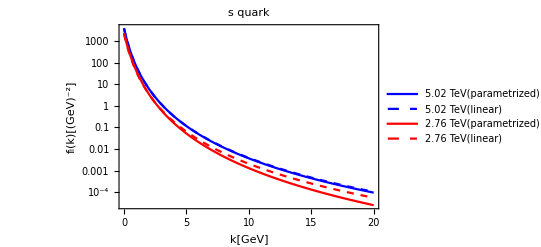

```mathematica
Show[{LogPlot[{s502[p],sg502[p],s276[p],sg276[p]},{p,0,20},PlotLegends->Placed[{"5.02 TeV(parametrized)","5.02 TeV(linear)","2.76 TeV(parametrized)","2.76 TeV(linear)"},{Right,Top}],PlotStyle->{Blue,{Blue,Dashed},Red,{Red,Dashed}},PlotLabel->"s quark"]},FrameLabel->{"k[GeV]","f_i(k)[(GeV)^-2]"},
LabelStyle->Directive[Black,Bold,12] ,FrameTicksStyle->{{Black,Thick},{Black,Thick}},Frame->True,FrameStyle->Thick]
```

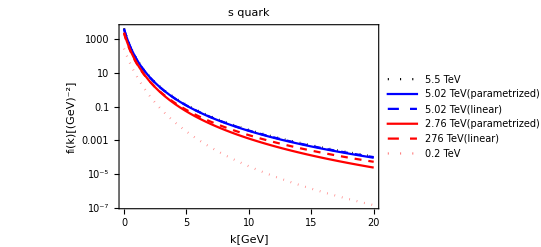

```mathematica
Show[{LogPlot[{s55[p],s502[p],sg502[p],s276[p],sg276[p],s02[p]},{p,0,20},PlotLegends->{"5.5 TeV","5.02 TeV(parametrized)","5.02 TeV(linear)","2.76 TeV(parametrized)","276 TeV(linear)","0.2 TeV"},PlotStyle->{{Black,Dotted},Blue,{Blue,Dashed},Red,{Red,Dashed},{Pink,Dotted}},PlotLabel->"s quark"]},FrameLabel->{"k[GeV]","f_i(k)[(GeV)^-2]"},
LabelStyle->Directive[Black,Bold,12] ,FrameTicksStyle->{{Black,Thick},{Black,Thick}},Frame->True,FrameStyle->Thick]
```